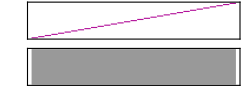

```mathematica
Sound[Table[SoundNote[k,0.5,"Harpsichord"],{k,-15,15}]]
```

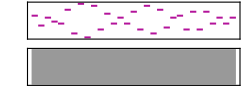

```mathematica
Sound[Table[SoundNote[Floor[5.5Sin[3t]+5.5]+Floor[7.5Sin[5t+π/3]^2+5.5],0.5,"Harpsichord"],{t,0,30}]]
```

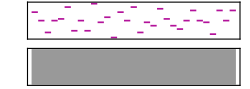

-Graphics-

```mathematica
Play[(10Sin[440 2Pi t])/(0.25+10Sin[1/12 2Pi t]^2)+(10Sin[440 2Pi t])/(0.25+10Sin[1/13.5 2Pi t]^2),{t,0,100}]
```

-Graphics-

```mathematica
Export["pendula.wav",Play[Sin[220 2Pi t]/(0.05+Sin[1/5 2Pi t]^2)+Sin[220 2Pi t]/(0.05+Sin[1/6 2Pi t]^2),{t,0,20}]]
```

pendula.wav

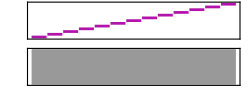

```mathematica
Sound[Table[SoundNote[i,0.1,"Violin"],{i,0,12}]]
```

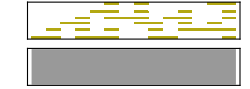

```mathematica
Sound[SoundNote[#,1/6,"Warm"]&/@(Pick[{0,5,9,12,16,21},#,1]&/@CellularAutomaton[30,{{1,0,0,0,0,0},0},13,{13,5}])]
```

```mathematica
SoundNote[DeleteCases[3 Range[31] Reverse[#], 0] - 48, .1] & /@ Transpose[CellularAutomaton[90, {{1}, 0}, 30]]
```

{SoundNote[{-45},0.1],SoundNote[{-42},0.1],SoundNote[{-39},0.1],SoundNote[{-42,-36},0.1],SoundNote[{-45,-33},0.1],SoundNote[{-36,-30},0.1],SoundNote[{-27},0.1],SoundNote[{-36,-30,-24},0.1],SoundNote[{-45,-33,-21},0.1],SoundNote[{-42,-36,-24,-18},0.1],SoundNote[{-39,-15},0.1],SoundNote[{-42,-24,-18,-12},0.1],SoundNote[{-45,-21,-9},0.1],SoundNote[{-24,-12,-6},0.1],SoundNote[{-3},0.1],SoundNote[{-24,-12,-6,0},0.1],SoundNote[{-45,-21,-9,3},0.1],SoundNote[{-42,-24,-18,-12,0,6},0.1],SoundNote[{-39,-15,9},0.1],SoundNote[{-42,-36,-24,-18,0,6,12},0.1],SoundNote[{-45,-33,-21,3,15},0.1],SoundNote[{-36,-30,-24,0,12,18},0.1],SoundNote[{-27,21},0.1],SoundNote[{-36,-30,0,12,18,24},0.1],SoundNote[{-45,-33,3,15,27},0.1],SoundNote[{-42,-36,0,6,12,24,30},0.1],SoundNote[{-39,9,33},0.1],SoundNote[{-42,0,6,24,30,36},0.1],SoundNote[{-45,3,27,39},0.1],SoundNote[{0,24,36,42},0.1],SoundNote[{45},0.1],SoundNote[{0,24,36,42},0.1],SoundNote[{-45,3,27,39},0.1],SoundNote[{-42,0,6,24,30,36},0.1],SoundNote[{-39,9,33},0.1],SoundNote[{-42,-36,0,6,12,24,30},0.1],SoundNote[{-45,-33,3,15,27},0.1],SoundNote[{-36,-30,0,12,18,24},0.1],SoundNote[{-27,21},0.1],SoundNote[{-36,-30,-24,0,12,18},0.1],SoundNote[{-45,-33,-21,3,15},0.1],SoundNote[{-42,-36,-24,-18,0,6,12},0.1],SoundNote[{-39,-15,9},0.1],SoundNote[{-42,-24,-18,-12,0,6},0.1],SoundNote[{-45,-21,-9,3},0.1],SoundNote[{-24,-12,-6,0},0.1],SoundNote[{-3},0.1],SoundNote[{-24,-12,-6},0.1],SoundNote[{-45,-21,-9},0.1],SoundNote[{-42,-24,-18,-12},0.1],SoundNote[{-39,-15},0.1],SoundNote[{-42,-36,-24,-18},0.1],SoundNote[{-45,-33,-21},0.1],SoundNote[{-36,-30,-24},0.1],SoundNote[{-27},0.1],SoundNote[{-36,-30},0.1],SoundNote[{-45,-33},0.1],SoundNote[{-42,-36},0.1],SoundNote[{-39},0.1],SoundNote[{-42},0.1],SoundNote[{-45},0.1]}

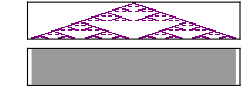

```mathematica
Sound[SoundNote[DeleteCases[3 Range[31] Reverse[#], 0] - 48, .1] & /@ Transpose[CellularAutomaton[90, {{1}, 0}, 30]]]
```

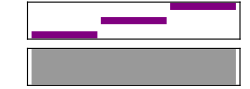

```mathematica
Sound[{SoundNote[0],SoundNote[2],SoundNote[4]}]
```

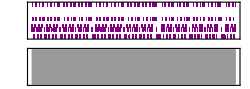

```mathematica
Sound[SoundNote[#]&/@{4,3,4,10,6,3,1,1,4,3,4,10,6,10,6,3,1,1,1,1,4,3,4,10,6,3,1,1,4,3,4,10,6,10,6,10,6,3,1,1,1,1,1,1,4,3,4,10,6,3,1,1,4,3,4,10,6,10,6,3,1,1,1,1,4,3,4,10,6,3,1,1,4,3,4,10,6,10,6,10,6,10,6,3,1,1,1,1,1,1,1,1,4,3,4,10,6,3,1,1,4,3,4,10,6,10,6,3,1,1,1,1,4,3,4,10,6,3,1,1,4,3,4,10,6,10,6,10,6,3,1,1,1,1,1,1,4,3,4,10,6,3,1,1,4,3,4,10,6,10,6,3,1,1,1,1,4,3,4,10,6,3,1,1,4,3,4,10,6,10,6,10,6,10,6,10,6,3,1,1,1,1,1,1,1,1,1,1,4,3,4,10,6,3,1,1,4,3,4,10,6,10,6,3,1,1,1,1,4,3,4,10,6,3,1,1,4,3,4,10,6,10,6,10,6,3,1,1,1,1,1,1,4,3,4,10,6,3,1,1,4,3,4,10,6,10,6,3,1,1,1,1,4,3,4,10,6,3,1,1,4,3,4,10,6,10,6,10,6,10,6,3,1,1,1,1,1,1,1,1,4,3,4,10,6,3,1,1,4,3,4,10,6,10,6,3,1,1,1,1,4,3,4,10,6,3,1,1,4,3,4,10,6,10,6,10,6,3,1,1,1,1,1,1,4,3,4,10,6,3,1,1,4,3,4,10,6,10,6,3,1,1,1,1,4,3,4,10,6,3,1,1,4,3,4,10,6,10,6,10,6,10,6,10,6,10,6,3,1,1,1,1,1,1,1,1,1,1,1,1,4,3,4,10,6,3,1,1,4,3,4,10,6,10,6,3,1,1,1,1,4,3,4,10,6,3,1,1,4,3,4,10,6,10,6,10,6,3,1,1,1,1,1,1,4,3,4,10,6,3,1,1,4,3,4,10,6,10,6,3,1,1,1,1,4,3,4,10,6,3,1,1,4,3,4,10,6,10,6,10,6,10,6,3,1,1,1,1,1,1,1,1,4,3,4,10,6,3,1,1,4,3,4,10,6,10,6,3,1,1,1,1,4,3,4,10,6,3,1,1,4,3,4,10,6,10,6,10,6,3,1,1,1,1,1,1,4,3,4,10,6,3,1,1,4,3,4,10,6,10,6,3,1,1,1,1,4,3,4,10,6,3,1,1,4,3,4,10,6,10,6,10,6,10,6,10,6,3,1,1,1,1,1,1,1,1,1,1,4,3,4,10,6,3,1,1,4,3,4,10,6,10,6,3,1,1,1,1,4,3,4,10,6,3,1,1,4,3,4,10},100]
```

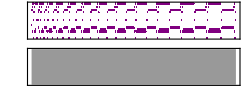

```mathematica
Sound[SoundNote[#-10]&/@{10,22,24,5,27,0,14,20,24,5,27,5,7,27,0,14,27,0,14,20,      8,22,24,5,27,0,14,20,24,5,27,5,7,27,5,27,0,14,20,8,8,22,8,22,24,5,27,0,14,20,24,5,27,5,7,27,5,7,27,5,27,0,14,20,8,8,22,8,8,22,8,22,24,5,27,0,14,20,24,5,27,5,7,27,5,7,27,5,7,27,5,27,0,14,20,8,8,22,8,8,22,8,8,22,8,22,24,5,27,0,14,20,24,5,27,5,7,27,5,7,27,5,7,27,5,7,27,5,27,0,14,20,8,8,22,8,8,22,8,8,22,8,8,22,8,22,24,5,27,0,14,20,24,5,27,5,7,27,5,7,27,5,7,27,5,7,27,5,7,27,5,27,0,14,20,8,8,22,8,8,22,8,8,22,8,8,22,8,8,22,8,22,24,5,27,0,14,20,24,5,27,5,7,27,5,7,27,5,7,27,5,7,27,5,7,27,5,7,27,5,27,0,14,20,8,8,22,8,8,22,8,8,22,8,8,22,8,8,22,8,8,22,8,22,24,5,27,0,14,20,24,5,27,5,7,27,5,7,27,5,7,27,5,7,27,5,7,27,5,7,27,5,7,27,5,27,0,14,20,8,8,22,8,8,22,8,8,22,8,8,22,8,8,22,8,8,22,8,8,22,8,22,24,5,27,0,14,20,24,5,27,5,7,27,5,7,27,5,7,27,5,7,27,5,7,27,5,7,27,5,7,27,5,7,27,5,27,0,14,20,8,8,22,8,8,22,8,8,22,8,8,22,8,8,22,8,8,22,8,8,22,8,8,22,8,22,24,5,27,0,14,20,24,5,27,5,7,27,5,7,27,5,7,27,5,7,27,5,7,27,5,7,27,5,7,27,5,7,27,5,7,27,5,27,0,14,20,8,8,22,8,8,22,8,8,22,8,8,22,8,8,22,8,8,22,8,8,22,8,8,22,8,8,22,8,22,24,5,27,0,14,20,24,5,27,5,7,27,5,7,27,5,7,27,5,7,27,5,7,27,5,7,27,5,7,27,5,7,27,5,7,27,5,7,27,5,27,0,14,20,8,8,22,8,8,22,8,8,22,8,8,22,8,8,22,8,8,22,8,8,22,8,8,22,8,8,22,8,8,22,8,22,24,5,27,0,14,20,24,5,27,5,7,27,5,7,27,5,7,27,5,7,27,5,7,27,5,7,27,5,7,27,5,7,27,5,7,27,5,7,27,5,7,27,5,27,0,14,20,8,8,22,8,8,22,8,8,22,8,8,22,8,8,22,8,8,22,8,8,22,8,8,22,8,8,22,8,8,22,8,8,22,8,22,24,5,27,0,14,20},100]
```